```mathematica
selldate= {{2010,1,15},{2010,2,18},{2010,5,4},{2010,5,12}};
```

```mathematica
net ={100,150,175,140};
```

```mathematica
trades={{{{2010,1,14},28.69286157666046},{{2010,1,15},28.802756276404608}},{{{2010,2,10},26.745129151291515},{{2010,2,18},27.532485586162714}},{{{2010,2,22},27.632201377108075},{{2010,5,4},35.894830678830985}},{{{2010,5,6},34.65488162436548},{{2010,5,12},35.400814987218126}}}
```

{{{{2010,1,14},28.6929},{{2010,1,15},28.8028}},{{{2010,2,10},26.7451},{{2010,2,18},27.5325}},{{{2010,2,22},27.6322},{{2010,5,4},35.8948}},{{{2010,5,6},34.6549},{{2010,5,12},35.4008}}}

```mathematica
selldate = Transpose[trades][[2]][[All,1]]
```

{{2010,1,15},{2010,2,18},{2010,5,4},{2010,5,12}}

```mathematica
buydate=Transpose[trades][[1]][[All,1]]
```

{{2010,1,14},{2010,2,10},{2010,2,22},{2010,5,6}}

```mathematica
buyprice=Transpose[trades][[1]][[All,2]]
```

{28.6929,26.7451,27.6322,34.6549}

```mathematica
sellprice=Transpose[trades][[2]][[All,2]]
```

{28.8028,27.5325,35.8948,35.4008}

```mathematica
grosProfit=30000;grosLoss=23100;maxDD=1200;netReturn=8.53;
```

```mathematica
aar=8;
```

```mathematica
performance=
Column[
{
Style["Performance",FontSize->14,Bold],
Grid[
{
{
"Net Profit",
"Gros Profit",
"Gros Loss",
"Maximum Drawdown",
"Profit Factor",
"Recovery Factor"
},
{
Row[{Quantity[grosProfit-grosLoss,"Euros"],"(",netReturn,"%)"}],
Quantity[grosProfit,"Euros"],
Quantity[grosLoss,"Euros"],
Quantity[maxDD,"Euros"],
N@grosProfit/grosLoss,
N@(grosProfit-grosLoss)/maxDD
}
},
Background->Lighter[Gray, 0.9],
Frame->All
],
Grid[
{
{
"Annual Average Return",
"Days in Market",
"Risc Adjusted Return",
"Calmar Ratio"
},
{
StringJoin[ToString[80.08],"%"],
StringJoin[ToString[31./127 100],"%"],
StringJoin[ToString[85.08],"%"],
StringJoin[ToString[15.08],"%"]}
},
Background->Lighter[Gray, 0.9],
Frame->All
],
Grid[
{
{
"Buy & Hold Profit",
"Anual Average Buy & Hold",
"Buy & Hold Index"
},
{
StringJoin[ToString[80.08],"%"],
StringJoin[ToString[31./127 100],"%"],
StringJoin[ToString[85.08],"%"]
}
},
Background->Lighter[Gray, 0.9],Frame->All
],
Grid[
{
{
"Total comissions",
"Total slippage",
"Comissions Index"
},
{
StringJoin[ToString[80.08],"%"],
StringJoin[ToString[31./127 100],"%"],
StringJoin[ToString[85.08],"%"]
}
},
Background->Lighter[Gray, 0.9],Frame->All
]
},
Frame->True, Alignment->Center,Background->Lighter[Gray, 0.5],BaseStyle->{FontFamily->"Arial"}
]
```

Performance
Net Profit | Gros Profit | Gros Loss | Maximum Drawdown | Profit Factor | Recovery Factor
6900 €(8.53%) | 30000 € | 23100 € | 1200 € | 1.2987 | 5.75
Annual Average Return | Days in Market | Risc Adjusted Return | Calmar Ratio
80.08% | 24.4094% | 85.08% | 15.08%
Buy & Hold Profit | Anual Average Buy & Hold | Buy & Hold Index
80.08% | 24.4094% | 85.08%
Total comissions | Total slippage | Comissions Index
80.08% | 24.4094% | 85.08%

```mathematica
performance
```

Performance
Net Profit | Gros Profit | Gros Loss | Maximum Drawdown | Profit Factor | Recovery Factor
6900 €(8.53%) | 30000 € | 23100 € | 1200 € | 1.2987 | 5.75
Annual Average Return | Days in Market | Risc Adjusted Return | Calmar Ratio
80.08% | 24.4094% | 85.08% | 15.08%
Buy & Hold Profit | Anual Average Buy & Hold | Buy & Hold Index
80.08% | 24.4094% | 85.08%
Total comissions | Total slippage | Comissions Index
80.08% | 24.4094% | 85.08%

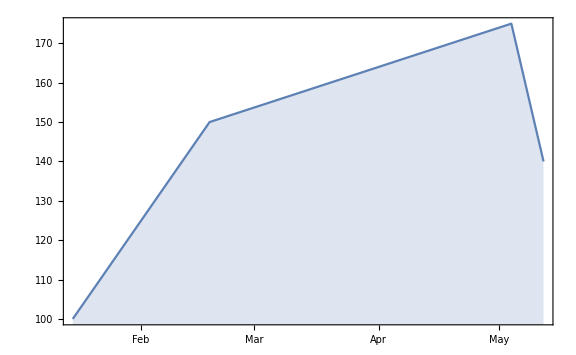
Equity plot:
-Graphics-

```mathematica
plt=Grid[
{{Style["Equity plot:",FontFamily->"Arial"]},
{DateListPlot[Transpose[{selldate,net}],Joined->True,
Filling->0,ImageSize->Large,PlotRange->Full]}}
]
```

```mathematica
table=
Transpose[
{Join[{Style["BuyDate",FontFamily->"Arial"]},DateString[#,"ISODate"]&/@buydate],
Join[{Style["BuyPrice",FontFamily->"Arial"]},buyprice],
Join[{Style["SellDate",FontFamily->"Arial"]},DateString[#,"ISODate"]&/@selldate],
Join[{Style["SellPrice",FontFamily->"Arial"]},sellprice]}
]
```

{{BuyDate,BuyPrice,SellDate,SellPrice},{2010-01-14,28.6929,2010-01-15,28.8028},{2010-02-10,26.7451,2010-02-18,27.5325},{2010-02-22,27.6322,2010-05-04,35.8948},{2010-05-06,34.6549,2010-05-12,35.4008}}

```mathematica
Column[{plt,performance,cost,com,lwt,llt,pos,neg,eq,curr,TableForm[table]},
Frame->All]
```

Equity plot:
-Graphics-
Performance
Net Profit | Gros Profit | Gros Loss | Maximum Drawdown | Profit Factor | Recovery Factor
6900 € | 30000 € | 23100 € | 23100 € | 1.2987 | 1.2987
Annual Average Return | Days in Market | Risc Adjusted Return | Calmar Ratio
80.08% | 24.4094% | 85.08% | 15.08%
Buy & Hold Profit | Anual Average Buy & Hold | Buy & Hold Index
80.08% | 24.4094% | 85.08%
cost
com
lwt
llt
pos
neg
eq
curr
BuyDate | BuyPrice | SellDate | SellPrice
2010-01-14 | 28.6929 | 2010-01-15 | 28.8028
2010-02-10 | 26.7451 | 2010-02-18 | 27.5325
2010-02-22 | 27.6322 | 2010-05-04 | 35.8948
2010-05-06 | 34.6549 | 2010-05-12 | 35.4008

```mathematica
{san,bbva}=<<"C:\\Users\\fabregas.TCMM\\Google Drive\\Borsa\\Borsa mat\\Workspace\\stock.mc"
```

{SAN.MC
from  Mon 1 Jan 2007  to  Fri 21 Oct 2016
2557  barsStock Object,BBVA.MC
from  Mon 1 Jan 2007  to  Fri 21 Oct 2016
2557  barsStock Object}

```mathematica
{san,bbva}=<<"C:\\Users\\Joan\\Google Drive\\Borsa\\Borsa mat\\Workspace\\stock.mc"
```

{SAN.MC
from  Mon 1 Jan 2007  to  Fri 21 Oct 2016
2557  barsStock Object,BBVA.MC
from  Mon 1 Jan 2007  to  Fri 21 Oct 2016
2557  barsStock Object}

```mathematica
par=Strategy["ParabolicStopAndReversal",{0.005,0.5}]
```

ParabolicStopAndReversal  {0.005,0.5}
 
 Strategy Object

```mathematica
td2=BackTest[san,par,"EntryPrices"->{"Median","Medium"},"ExitPrices"->{"Median","Medium"}]
```

SAN.MC  with  ParabolicStopAndReversal
from  Tue 2 Jan 2007  to  Fri 21 Oct 2016
51  tradesBackTest Object

```mathematica
td3=BackTest[bbva,par]
```

BBVA.MC  with  ParabolicStopAndReversal
from  Tue 2 Jan 2007  to  Fri 21 Oct 2016
53  tradesBackTest Object

```mathematica
td2["Performance"]
```

daqgk_shm36FrontEndObject[LinkObject["daqgk_shm", 3, 1]]36Untitled-10

```mathematica
td3["Performance"]
```

daqgk_shm34FrontEndObject[LinkObject["daqgk_shm", 3, 1]]34Untitled-9

```mathematica
GenerateDocument["BTTemplate.nb",td2["Performance"]]
```

qer59_shm30FrontEndObject[LinkObject["qer59_shm", 3, 1]]30Untitled-9

```mathematica
numForm=ToString@NumberForm[#,{10,2},ExponentFunction->(If[-10<#<10,Null,#]&)]&
```

ToString[Slot[1.00]]&

```mathematica
numForm[N@Pi]
```

3.14

```mathematica
%
```

3.14

```mathematica
perf=td2["Performance"][[2]];
```

```mathematica
p=Column[
{
Style["Overall Performance",FontSize->14,Bold],
Grid[
Transpose@perf[[1,1]],
Background->Lighter[Gray, 0.9],
Frame->All
],
Grid[
Transpose@perf[[1,2]],
Background->Lighter[Gray, 0.9],
Frame->All
],
Grid[
Transpose@perf[[1,3]],
Background->Lighter[Gray, 0.9],Frame->All
],
Style["Trades Performance",FontSize->14,Bold],
Grid[
Transpose@perf[[2,1]],
Background->Lighter[Gray, 0.9],Frame->All
],
Grid[
Transpose@perf[[2,2]],
Background->Lighter[Gray, 0.9],Frame->All
],
Grid[
Transpose@perf[[2,3]],
Background->Lighter[Gray, 0.9],Frame->All
],
Grid[
Transpose@perf[[2,4]],
Background->Lighter[Gray, 0.9],Frame->All
],
Style["Slippage",FontSize->14,Bold],
Grid[
Transpose@perf[[3,1]],
Background->Lighter[Gray, 0.9],Frame->All
]
},
Frame->True, Alignment->Center,Background->Lighter[Gray, 0.5],BaseStyle->{FontFamily->"Arial"}
];
```

```mathematica
d=DateListPlot[{td2["Performance"][[3,1]],td2["Performance"][[3,2]],td2["Performance"][[3,3]]}];
```

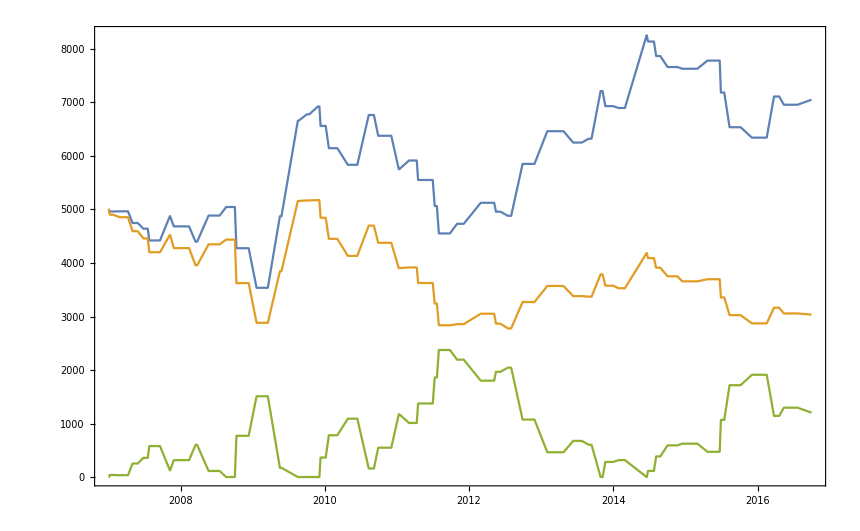
Overall Performance
Net Profit | Gross Profit | Gross Loss | Maximum Drawdown | Profit Factor | Recovery Factor
2051.35(41.03%) | 11074.54(221.49%) | 9023.18(180.46%) | 2373.90(34.27%) | 1.23 | 0.86
Annual Average Return | Days in Market | Risc Adjusted Return | Mar Ratio | Total commissions | Commission Index
3.59% | 50.93% | 7.04% | 0.10 | 0.00 | 0.00
Buy & Hold Profit | Annual Average BH Return | Buy & Hold Index
-1661.54(-33.23%) | -4.06% | 1.88
Trades Performance
Number of Trades | Winning Trades | Lossing Trades | Average Trades/Year | Sharpe Ratio of Trades
50 | 20(40.00%) | 30(60.00%) | 5.13 | 0.11
Average Trade | Average Profit Trade | Largest Profit Trade Return | Average Loss Trade | Largest Loss Trade Return | Payoff Ratio
41.03(0.69%) | 553.727(10.26%) | 37.80% | 300.773(5.22%) | 17.29% | 1.84
Average Days Trade | Average Days Profit Trade | Average Days Loss Trade | Average Eficiency
36.26 | 56.30 | 22.90 | -15.61%
Average MFE | Average Profit MFE | Average Loss MFE | Average MAE | Average Profit MAE | Average Loss MAE
9.01% | 17.07% | 3.64% | -5.85% | -3.77% | -7.24%
Slippage
Net profit | Maximum Drawdown | Profit Factor | Recovery Factor | Average Trade | Winning Trades | Payoff Ratio | Average Eficiency
-1965.39(-39.31%) | 2398.09(46.34%) | 0.76 | -0.82 | -39.31(-0.99%) | 17.(34.00%) | 1.47 | -30.06%
-Graphics-

```mathematica
Column[{p,d}]
```

```mathematica
{daysTrade,netTradeReturns,mfe,mae,win}=td2["Performance"][[3,4]];
```

```mathematica
TabView[
{"MFE-MAE"-> ListPlot[Apply[Style,Transpose@{Transpose@{mfe,-mae},win},1]],
"Returns-ETD"-> ListPlot[Apply[Style,Transpose@{Transpose@{netTradeReturns,mfe-netTradeReturns},win},1]],
"Days-Eficiency"-> ListPlot[Apply[Style,Transpose@{Transpose@{daysTrade,netTradeReturns/(mfe-mae)},win},1]]}
]
```

123

```mathematica
{san,bbva}=<<"C:\\Users\\fabregas.TCMM\\Google Drive\\Borsa\\Borsa mat\\Workspace\\stock.mc"
```

Get::noopen: Cannot open C:\Users\fabregas.TCMM\Google Drive\Borsa\Borsa mat\Workspace\stock.mc.

Set::shape: Lists {san,bbva} and $Failed are not the same shape.

$Failed

```mathematica
{san,bbva}=<<"C:\\Users\\Joan\\Google Drive\\Borsa\\Borsa mat\\Workspace\\stock.mc"
```

{SAN.MC
from  Mon 1 Jan 2007  to  Fri 21 Oct 2016
2557  barsStock Object,BBVA.MC
from  Mon 1 Jan 2007  to  Fri 21 Oct 2016
2557  barsStock Object}

```mathematica
par=Strategy["ParabolicStopAndReversal",{0.005,0.5}]
```

ParabolicStopAndReversal  {0.005,0.5}
 
 Strategy Object

```mathematica
td2=BackTest[san,par,"EntryPrices"->{"Median","Medium"},"ExitPrices"->{"Median","Medium"}]
```

SAN.MC  with  ParabolicStopAndReversal
from  Tue 2 Jan 2007  to  Fri 21 Oct 2016
51  tradesBackTest Object

```mathematica
s=td2["Performance"][[3,5]];t=td2["Performance"][[3,6]];
```

```mathematica
{Length[s],Length[t]}
```

{2557,50}

```mathematica
index=(Flatten@{Position[s[[All,1]],t[[#,1]]],Position[s[[All,1]],t[[#,4]]]})&/@Range[Length[t]]
```

{{3,4},{5,6},{18,42},{72,89},{107,128},{144,150},{188,224},{225,238},{293,316},{322,364},{404,427},{459,465},{509,537},{578,621},{627,686},{690,720},{728,760},{765,769},{787,799},{830,867},{901,943},{961,977},{1025,1050},{1053,1088},{1115,1120},{1172,1178},{1187,1193},{1233,1259},{1283,1345},{1393,1400},{1416,1443},{1455,1497},{1539,1586},{1644,1679},{1711,1735},{1746,1778},{1786,1796},{1823,1843},{1867,1945},{1946,1950},{1972,1979},{1994,2021},{2057,2073},{2128,2165},{2209,2213},{2226,2245},{2285,2326},{2379,2406},{2424,2442},{2491,2542}}

```mathematica
Length[index]
```

50

```mathematica
For[i=1,i≤Length[t],i++,
s[[index[[i,1]]]]=Labeled[s[[index[[i,1]]]],Column[{"   ↑","Entry"}]];
s[[index[[i,2]]]]=Labeled[s[[index[[i,2]]]],Column[{"Exit","  ↓"}],Above]
]
```

```mathematica
Manipulate[
TradingChart[s[[If[index[[i,1]]-5>0,index[[i,1]]-5,1];;index[[i,2]]+5]]],
{{i,3},Range[Length[t]]}]
```

Part::partd: Part specification index⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification index⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::span: If[-5+index⟦1,1⟧>0,index⟦FE`i$$35,1⟧-5,1];;5+index⟦1,2⟧ is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

TradingChart::ldata: s⟦If[-5+index⟦1,1⟧>0,index⟦FE`i$$35,1⟧-5,1];;5+index⟦1,2⟧⟧ is not a valid dataset or list of datasets.

Part::partd: Part specification index⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification index⟦1,2⟧ is longer than depth of object.

Part::span: If[-5+index⟦1,1⟧>0,index⟦FE`i$$35,1⟧-5,1];;5+index⟦1,2⟧ is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

TradingChart::ldata: s⟦If[-5+index⟦1,1⟧>0,index⟦FE`i$$35,1⟧-5,1];;5+index⟦1,2⟧⟧ is not a valid dataset or list of datasets.